# SubsetFromIndex

Get the subset with the given index and length

## Definition

```mathematica
SubsetFromIndex[index_Integer,len_Integer]:= Module[{subset,total, x},
subset=Table[0,{len}];
total=index;
Do[subset[[in]]=Ceiling[x/.Flatten[
NSolve[{Product[(x-n+1)/n,{n,1,in}]==total,x>0},x]]]-1;
total=total-Binomial[subset[[in]],in],
{in,len,1,-1}];
subset];
```

## Documentation

### Usage

SubsetFromIndex[index,len]

returns a subset of length len with given index.

### Details & Options

Subsets are considered to be lists {a_1,a_2,…,a_k} such that the a_i are non-negative integers and strictly increasing.

Subsets are sorted by their reverse; {1,2,3} comes before {0,1,4}.

For any subset, a unique index n can be defined via n=∑_(j=1)^k Binomial[a_j, j].

For example: subset {2,4,6} has index (2
1)+(4
2)+(6
3)+1=29.

## Examples

### Basic Examples

Give the first ten 3-subsets:

```mathematica
Table[SubsetFromIndex[index,3],{index,1,10}]
```

{{0,1,2},{0,1,3},{0,2,3},{1,2,3},{0,1,4},{0,2,4},{1,2,4},{0,3,4},{1,3,4},{2,3,4}}

The following code gives the same 3-subset sequence:

```mathematica
SortBy[Subsets[Range[0,4],{3}],Reverse]
```

{{0,1,2},{0,1,3},{0,2,3},{1,2,3},{0,1,4},{0,2,4},{1,2,4},{0,3,4},{1,3,4},{2,3,4}}

The function can return subsets of a large index:

```mathematica
Table[SubsetFromIndex[index,3],{index,182000,182400,47}]
```

{{98,101,103},{44,102,103},{91,102,103},{0,9,104},{5,13,104},{10,16,104},{6,19,104},{14,21,104},{18,23,104}}

The function can return the subset of a given index for various lengths:

```mathematica
Table[SubsetFromIndex[2019,len],{len,2,9}]
```

{{2,64},{16,22,23},{5,8,11,16},{0,1,3,6,14},{2,3,5,7,10,13},{0,1,3,7,8,10,13},{0,5,6,7,9,10,11,13},{1,2,3,4,5,6,7,9,14}}

### Scope

Some binomial representations of the number 321:

```mathematica
Column[Row[Riffle[Table[TraditionalForm[Binomial[(ToString/@#)[[n]],ToString[n]]],{n,1,Length[#]}],"+"]]&/@Table[SubsetFromIndex[321,n],{n,2,7}], Alignment-> Center]
```

Binomial[20, 1]+Binomial[25, 2]
Binomial[6, 1]+Binomial[8, 2]+Binomial[13, 3]
Binomial[5, 1]+Binomial[7, 2]+Binomial[9, 3]+Binomial[10, 4]
Binomial[3, 1]+Binomial[5, 2]+Binomial[6, 3]+Binomial[7, 4]+Binomial[10, 5]
Binomial[3, 1]+Binomial[4, 2]+Binomial[5, 3]+Binomial[7, 4]+Binomial[8, 5]+Binomial[10, 6]
Binomial[2, 1]+Binomial[3, 2]+Binomial[6, 3]+Binomial[7, 4]+Binomial[8, 5]+Binomial[9, 6]+Binomial[10, 7]

Here are some 2-subsets with their indices to show their structure:

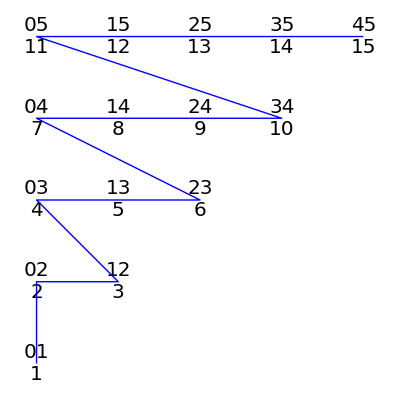

```mathematica
doubles=Table[{SubsetFromIndex[index,2],index},{index,1,15}];
Graphics[{Text[Style[Column[{StringJoin[ToString/@#[[1]]],#[[2]]},
Alignment-> Center],20],#[[1]]]&/@doubles,Blue, Line[First/@doubles]}]
```

The structure of 3-subsets in 3D:

```mathematica
triples=Table[{SubsetFromIndex[index,3],index},{index,1,20}];
Graphics3D[{Text[Style[Column[{StringJoin[ToString/@#[[1]]],#[[2]]},
Alignment-> Center],20],#[[1]]]&/@triples,Blue, Line[First/@triples]}]
```

-Graphics3D-

### Neat Examples

Find the trillionth numbers with binary weights eight to twelve:

```mathematica
Column[Table[Total[2^SubsetFromIndex[10^12,weight]],{weight,8,12}]]
```

5322104319612281937559310120997879808
9908507465330418439078608896
75706599607482756112899
40208150669450806344
307942558190157825

## Source & Additional Information

### Contributed By

Ed Pegg Jr

### Keywords

subset

index

tuple

### Categories

3D Visualization |  Accessibility
 Accessing External Services & APIs |  Associations
 Astronomical Computation & Data |  Background & Scheduled Tasks
 Calculus |  Calling External Programs
 Cloud & Deployment |  Cloud Functions & Deployment
 Code as Data |  Color Processing
 Computational Geometry |  Computation on Graphs
 Computer Vision |  Control Objects
 Core Language & Structure |  Creating Form Interfaces & Apps
 Cryptography |  Cultural Data
 Data Manipulation & Analysis |  Data Structures
 Data Transforms and Smoothing |  Data Visualization
 Date & Time |  Decorations
 Differential Geometry |  Dimension Reduction
 Discrete Mathematics |  Dynamic Interactivity Language
 Engineering Data & Computation |  Error Handling
 Expressions |  External Interfaces & Connections
 External Language Interfaces |  File Operations
 Financial Data & Computation |  Front End Utilities
 Functional Programming |  Function Visualization
 Games |  Geographic Data and Entities
 Geographic Data & Computation |  Geographic Visualization
 Geometric Region Properties |  Geometric Transforms
 Geometry |  Graph Construction & Representation
 Graph Properties & Measurements |  Graphs & Networks
 Graph Visualization |  Handling Arrays of Data
 Higher Mathematical Computation |  Image Filtering & Neighborhood Processing
 Image Processing & Analysis |  Images
 Importing and Exporting |  Interactive Manipulation
 Iterated Maps & Fractals |  Just For Fun
 Knowledge Representation & Natural Language |  Layout & Tables
 Life Sciences & Medicine: Data & Computation |  Linguistic Data
 List Manipulation |  Logic & Boolean Algebra
 Low-Level Notebook Programming |  Machine Learning
 Maps & Cartography |  Mathematical Functions
 Matrices and Linear Algebra |  Molecular Structure & Computation
 Natural Language Processing |  Neural Networks
 Notebook Basics |  Notebook Document Generation
 Notebook Documents & Presentation |  Notebook Formatting & Styling
 Number Theory |  Numeric Approximation
 Optimization |  Parallel Computing
 Persistent Storage |  Physics & Chemistry: Data and Computation
 Plane Geometry |  Polynomial Algebra
 Precollege Education |  Presentations with the Wolfram System
 Probability & Statistics |  Programming Utilities
 Random Stuff |  Real & Complex Analysis
 Recreational Math |  Repository Tools
 RepositoryTools |  Rules & Patterns
 Scientific and Medical Data & Computation |  Scientific Data Analysis
 Segmentation Analysis |  Sequence Analysis
 Shortcuts and Idioms |  Signal Processing
 Social, Cultural & Linguistic Data |  Social Data
 Solid Geometry |  Sound & Video
 Statistical Data Analysis |  String Manipulation
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Text Analysis
 Text Manipulation |  Theorem Proving
 Time-Related Computation |  Time Series Processing
 Topology |  Tuning & Debugging
 Units & Quantities |  User Interface Construction
 Viewers and Annotation |  Visualization & Graphics
 Weather Data |  Web Operations
 Wolfram Physics Project |  Wolfram System Setup
 Working with Paclets |

### Related Symbols

Subsets

Binomial

Tuples

### Related Resource Objects

OrderedTupleIndex

OrderedTupleFromIndex

PermutationIndex

PermutationFromIndex

SubsetIndex

TupleIndex

TupleFromIndex

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
SubsetFromIndex[100,4]
```

{3,4,6,8}

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.